# Наилучшее среднеквадратичное приближение (Лагерр)

Выполнил:Сайков Константин
																																	Группа:ПМ1801

```mathematica
Lagerr2[k_,lag1_,lag2_,n_,alfa_]:=Module[{},If[n≥  k,
If[k==0,1,lag1],Lagger2[k,1/(n+1)*((2n+1+alfa-x)*lag1-(n+alfa)*lag2),lag1,n+1,alfa] ]
]
a[fun_,n_,alfa_]:=Integrate[fun*ⅇ^-x*x^alfa*Lagerr2[n,1-x,1,1,alfa],{x,0,Infinity}];
approx[fun_,n_,alfa_]:=Total[Table[N@Lagerr2[k,1-x,1,1,alfa]*a[fun,k,alfa]//N,{k,0,n}]]//FullSimplify
```

```mathematica
polynomial=approx[x^5,5,0];
```

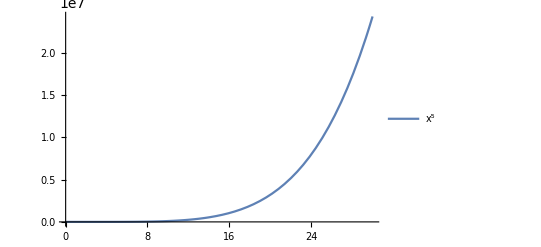

```mathematica
Plot[x^5,{x,0,30},PlotLegends->{"x^5"}]
```

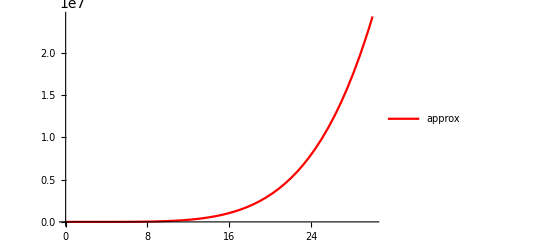

```mathematica
Plot[polynomial/.x->k,{k,0,30},PlotStyle->Red,PlotLegends->{"approx"}]
```

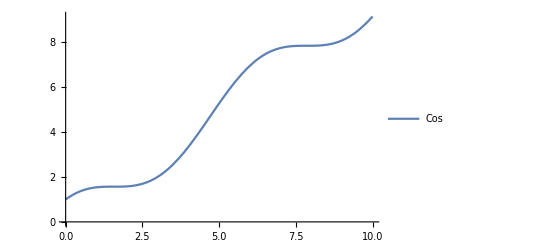

```mathematica
polynomial1=approx[Cos[x]+x,15,0];
Plot[Cos[x]+x,{x,0,10},PlotLegends->{"Cos"}]
```

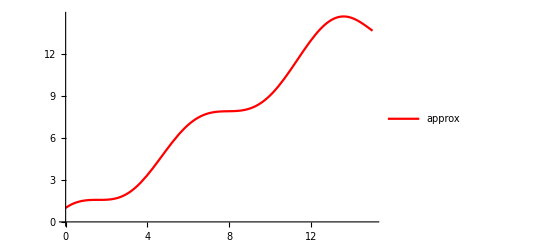

```mathematica
Plot[polynomial1/.x->k,{k,0,15},PlotStyle->Red,PlotLegends->{"approx"}]
```

A если повысить степень?

```mathematica
polynomial1=approx[Cos[x]+x,20,0];
```

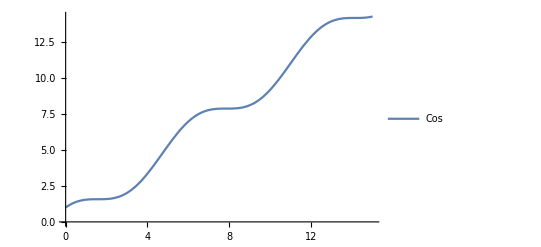

```mathematica
Plot[Cos[x]+x,{x,0,15},PlotLegends->{"Cos"}]
```

Теперь чуть больше похоже на то, что было

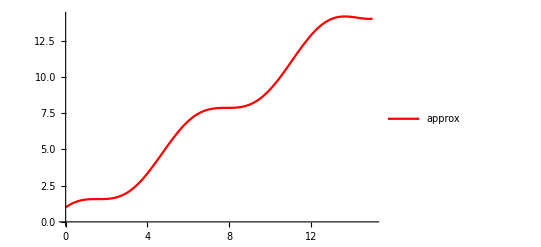

```mathematica
Plot[polynomial1/.x->k,{k,0,15},PlotStyle->Red,PlotLegends->{"approx"}]
```